```mathematica
Notebook for the polynomial method in the Schroedinger equation. 
This example is for the case of the hexagonal well of side 1
```

Defining initialization variables

```mathematica
size=55;
L=1;
```

Symbolic integral of the generic x^n y^m integral term

```mathematica
$Assumptions={m≥0&&m∈Integers,n≥0&&n∈Integers,x∈Reals,y∈Reals};
integral[n_,m_]=1/((1+n) (2+m+n))2^(-2-m-n)* 3^((1+m)/2) (1+(-1)^m) (1+(-1)^n) (1+2^(2+m+n) (1+n) Beta[1/2,1+m,1+n]);
AbsoluteTiming[intTablehex=ParallelTable[integral[i,j],{i,0,200},{j,0,200},Method->"CoarsestGrained",DistributedContexts->Automatic];]
MyIntegral[n_,m_]:=MyIntegral[n,m]=intTablehex[[n+1,m+1]]
SetAttributes[MyIntegral,Listable]
AbsoluteTiming[ParallelTable[MyIntegral[i,j],{i,0,200},{j,0,200}];]
```

{3.31745,Null}

{2.84015,Null}

Creating data folder

```mathematica
shape="hexagon";
folder="~/agr_tese/data/symbolic_new/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
reg=Polygon[CirclePoints[L,6]];
```

Defining normalization, scalar product, and Hamiltonian integration elements

```mathematica
coeffs[func_]:=coeffs[func]=GroebnerBasis`DistributedTermsList[func,{x,y},MonomialOrder->DegreeLexicographic][[1,All]]
MyNorm[func1_]:=√MyProd[func1,func1]

MyProd[func1_,func2_]:=Collect[(coeffs[func1[x,y]*func2[x,y]][[All,2]]).MyIntegral[coeffs[func1[x,y]*func2[x,y]][[All,1,1]],coeffs[func1[x,y]*func2[x,y]][[All,1,2]]],{x,y},Simplify]

Ham[f1_,f2_]:=(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])
En[func1_]:=Simplify[-1*(func1[[All,2]]).MyIntegral[func1[[All,1,1]],func1[[All,1,2]]]]
```

Finding the numerical eigenvalues for comparison

```mathematica
exact=(4Tan[π/6])/6*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,size];
```

```mathematica
(*AbsoluteTiming[Table[CoefficientRules[ϕn[5,x,y]*ϕn[7,x,y]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Simplify[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Expand[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]*)
```

Defining the initial function

```mathematica
ϕu[1,x_,y_]=(y-(√3)/2 L)*(y+(√3)/2 L)*(x-(√3)/3 y-L)*(x-(√3)/3 y+L)*(x+(√3)/3 y-L)*(x+(√3)/3 y+L);
ϕn[1,x_,y_]=Simplify[(1/(MyNorm[ϕu[1,#1,#2]&]))*ϕu[1,x,y]];
D[ϕn[1,x,y],{x,2}]+D[ϕn[1,x,y],{y,2}]//AbsoluteTiming;
Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]//AbsoluteTiming;
En[coeffs[Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]]]//AbsoluteTiming
```

{0.010106,344974/47505}

```mathematica
AbsoluteTiming[CoefficientRules[ϕn[1,x,y],{x,y}];]
AbsoluteTiming[AAA=GroebnerBasis`DistributedTermsList[ϕn[1,x,y],{x,y},MonomialOrder->DegreeLexicographic][[1,All]];]
```

{0.006904,Null}

{0.001675,Null}

```mathematica
f[m_,x_,y_]:=If[Mod[(m-1)-(Floor[√(m-1)])^2,2]==0,x^Floor[√(m-1)]*y^(((m-1)-(Floor[√(m-1)])^2)/2),x^(((m-1)-(Floor[√(m-1)])^2-1)/2)*y^Floor[√(m-1)]]
For[counter=2,counter<size+1,counter++,
ϕu[counter,x_,y_]=f[counter,x,y]*ϕn[1,x,y]-ParallelSum[MyProd[f[counter,x,y]*ϕn[1,#1,#2]&,ϕn[n,#1,#2]&]*ϕn[n,x,y],{n,1,counter-1},Method->"FinestGrained"];
ϕn[counter,x_,y_]=Simplify[ϕu[counter,x,y]/MyNorm[ϕu[counter,#1,#2]&]];
Print[counter]]//AbsoluteTiming
Basis[x_,y_]=Table[ϕn[i,x,y],{i,1,size}];
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

{2129.71,Null}

55

Uncomment this table for verification of the orthogonality of the basis

```mathematica
(*ortho=ParallelTable[MyProd[Basis[#1,#2][[b]]&,Basis[#1,#2][[c]]&],{b,1,size},{c,1,i},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];]
MatrixForm[orthofull]//Chop*)
```

Calculate the Hamiltonian matrix
It is Hermitian, so only the upper-triangular matrix is calculated

```mathematica
AbsoluteTiming[H=ParallelTable[Ham[ϕn[i,#1,#2]&,ϕn[j,#1,#2]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{8.71941,Null}

```mathematica
AbsoluteTiming[Hn=ParallelTable[coeffs[N[H[[i,j]],100]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{80.2762,Null}

```mathematica
AbsoluteTiming[H2=ParallelTable[En[Hn[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=MapThread[Join,{H2,Rest/@Flatten[Conjugate[H2],{{2},{1}}]}];]
MatrixForm[N[Hfull]]
```

{17.2719,Null}

{0.001114,Null}

(7.26185 | 0. | 0. | 0. | -1.08305 | -1.19638 | 0. | 0. | -0.627748 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.09149 | -1.07201 | 0. | 0. | -0.122084 | -0.684322 | 0. | 0. | -0.191519 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.81679 | -0.744271 | 0. | 0. | -0.202297 | -0.537127 | 0. | 0. | -0.12606 | -0.234109 | 0. | 0. | -0.0148031 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 18.1913 | 0. | 0. | 0. | 0. | 0. | 0.275311 | 0. | 0.588567 | 0. | 0. | 0. | 0.806386 | 0. | 0. | 0. | 0. | 0. | -1.03558 | 0. | 0. | 0. | -0.684717 | 0. | -1.13719 | 0. | 0. | 0. | 0.629391 | 0. | 0. | 0. | -0.0477269 | 0. | 0. | 0. | 0. | 0. | -0.962795 | 0. | 0. | 0. | -0.659805 | 0. | 0. | 0. | 0.00384115 | 0. | -1.2671 | 0. | 0. | 0. | 0.462299 | 0.
0. | 0. | 18.1913 | 0. | 0. | 0. | 0.287244 | 0. | 0. | 0. | 0.582837 | 0. | 0. | 0. | -1.61693 | 0. | 0. | 0. | 0.0606453 | 0. | 0. | 0. | 0.0567326 | 0. | 0. | 0. | -0.702725 | 0. | 0. | 0. | -1.73281 | 0. | 0. | 0. | -0.321476 | 0. | 0. | 0. | 0.0668327 | 0. | 0. | 0. | -0.152377 | 0. | 0. | 0. | 0.0727452 | 0. | 0. | 0. | -0.645551 | 0. | 0. | 0. | -1.43245
0. | 0. | 0. | 33.0359 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.3061 | 2.61734 | 0. | 0. | 0.226535 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.78532 | -1.52986 | 0. | 0. | 1.66896 | -1.20637 | 0. | 0. | 0.167048 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.60125 | -1.73367 | 0. | 0.
-1.08305 | 0. | 0. | 0. | 35.5759 | 2.80583 | 0. | 0. | 3.83283 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.0792 | 0.36576 | 0. | 0. | 4.43138 | 0.45588 | 0. | 0. | -0.497248 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.548891 | 0.00546769 | 0. | 0. | 3.76665 | -0.414431 | 0. | 0. | 0.219388 | -0.477819 | 0. | 0. | 0.271145 | 0. | 0. | 0. | 0. | 0. | 0.
-1.19638 | 0. | 0. | 0. | 2.80583 | 36.1353 | 0. | 0. | 0.882721 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.06447 | 7.1017 | 0. | 0. | 2.60054 | -2.61543 | 0. | 0. | 0.255813 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.06876 | 2.75872 | 0. | 0. | 1.5276 | -3.33391 | 0. | 0. | 0.448523 | -0.509403 | 0. | 0. | 0.293136 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.287244 | 0. | 0. | 0. | 57.645 | 0. | 0. | 0. | 3.8541 | 0. | 0. | 0. | 5.19294 | 0. | 0. | 0. | 17.7808 | 0. | 0. | 0. | 5.32145 | 0. | 0. | 0. | 0.177334 | 0. | 0. | 0. | 0.00171962 | 0. | 0. | 0. | -0.832121 | 0. | 0. | 0. | 9.6028 | 0. | 0. | 0. | 5.3368 | 0. | 0. | 0. | 1.19015 | 0. | 0. | 0. | -0.423815 | 0. | 0. | 0. | -1.11392
0. | 0.275311 | 0. | 0. | 0. | 0. | 0. | 51.5379 | 0. | 6.51475 | 0. | 0. | 0. | 7.34144 | 0. | 0. | 0. | 0. | 0. | 7.84657 | 0. | 0. | 0. | -1.3057 | 0. | 4.09129 | 0. | 0. | 0. | 5.13698 | 0. | 0. | 0. | 3.12376 | 0. | 0. | 0. | 0. | 0. | 0.229369 | 0. | 0. | 0. | -3.11563 | 0. | 0. | 0. | 0.245292 | 0. | 2.72732 | 0. | 0. | 0. | 3.4043 | 0.
-0.627748 | 0. | 0. | 0. | 3.83283 | 0.882721 | 0. | 0. | 79.7012 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 11.9131 | 3.33436 | 0. | 0. | 19.2899 | 18.1692 | 0. | 0. | 5.3271 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.55823 | -1.35989 | 0. | 0. | 14.2982 | 2.29785 | 0. | 0. | 8.25457 | 1.38649 | 0. | 0. | 1.90749 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.588567 | 0. | 0. | 0. | 0. | 0. | 6.51475 | 0. | 62.4179 | 0. | 0. | 0. | 10.145 | 0. | 0. | 0. | 0. | 0. | 2.61806 | 0. | 0. | 0. | -1.84952 | 0. | 17.3347 | 0. | 0. | 0. | 11.3481 | 0. | 0. | 0. | -0.12369 | 0. | 0. | 0. | 0. | 0. | 0.54723 | 0. | 0. | 0. | -1.50491 | 0. | 0. | 0. | 0.602912 | 0. | 5.54469 | 0. | 0. | 0. | 9.98523 | 0.
0. | 0. | 0.582837 | 0. | 0. | 0. | 3.8541 | 0. | 0. | 0. | 63.5658 | 0. | 0. | 0. | 0.147603 | 0. | 0. | 0. | 3.94773 | 0. | 0. | 0. | 3.57831 | 0. | 0. | 0. | 21.0368 | 0. | 0. | 0. | -4.76007 | 0. | 0. | 0. | 0.322855 | 0. | 0. | 0. | 2.36944 | 0. | 0. | 0. | 2.52946 | 0. | 0. | 0. | 1.73586 | 0. | 0. | 0. | 11.6214 | 0. | 0. | 0. | -5.6604
0. | 0. | 0. | 5.3061 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 91.4387 | 13.1919 | 0. | 0. | 10.7508 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 37.1125 | 2.44929 | 0. | 0. | 13.0164 | 3.69502 | 0. | 0. | -0.0800222 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 21.6542 | 0.156208 | 0. | 0.
0. | 0. | 0. | 2.61734 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 13.1919 | 83.4363 | 0. | 0. | 10.284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 13.145 | 19.9915 | 0. | 0. | 12.4077 | 0.63684 | 0. | 0. | 4.45976 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.83495 | 5.95793 | 0. | 0.
0. | 0.806386 | 0. | 0. | 0. | 0. | 0. | 7.34144 | 0. | 10.145 | 0. | 0. | 0. | 118.663 | 0. | 0. | 0. | 0. | 0. | 14.6735 | 0. | 0. | 0. | 14.9953 | 0. | 18.5809 | 0. | 0. | 0. | 49.6381 | 0. | 0. | 0. | 15.0257 | 0. | 0. | 0. | 0. | 0. | 2.95202 | 0. | 0. | 0. | 5.14537 | 0. | 0. | 0. | -1.30768 | 0. | 12.2467 | 0. | 0. | 0. | 30.7231 | 0.
0. | 0. | -1.61693 | 0. | 0. | 0. | 5.19294 | 0. | 0. | 0. | 0.147603 | 0. | 0. | 0. | 107.044 | 0. | 0. | 0. | 16.1232 | 0. | 0. | 0. | 21.1186 | 0. | 0. | 0. | 2.48176 | 0. | 0. | 0. | 28.5017 | 0. | 0. | 0. | 2.62612 | 0. | 0. | 0. | 7.9681 | 0. | 0. | 0. | 18.3897 | 0. | 0. | 0. | 10.4854 | 0. | 0. | 0. | -3.37087 | 0. | 0. | 0. | 7.69159
0. | 0. | 0. | 0.226535 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.7508 | 10.284 | 0. | 0. | 149.46 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 24.0089 | 14.4273 | 0. | 0. | 39.0879 | 50.7847 | 0. | 0. | 14.0536 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 12.0844 | -0.297941 | 0. | 0.
-1.09149 | 0. | 0. | 0. | 6.0792 | 2.06447 | 0. | 0. | 11.9131 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 98.2111 | 1.0654 | 0. | 0. | 19.0319 | 6.07996 | 0. | 0. | -2.19382 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 34.8511 | -0.464499 | 0. | 0. | 21.9082 | 1.624 | 0. | 0. | 0.355151 | -1.71851 | 0. | 0. | 1.63563 | 0. | 0. | 0. | 0. | 0. | 0.
-1.07201 | 0. | 0. | 0. | 0.36576 | 7.1017 | 0. | 0. | 3.33436 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.0654 | 103.072 | 0. | 0. | 5.87391 | 0.416376 | 0. | 0. | 4.32149 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.847602 | 44.5684 | 0. | 0. | 4.78716 | -7.57014 | 0. | 0. | 2.81584 | 1.89583 | 0. | 0. | 2.71031 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0606453 | 0. | 0. | 0. | 17.7808 | 0. | 0. | 0. | 3.94773 | 0. | 0. | 0. | 16.1232 | 0. | 0. | 0. | 150.196 | 0. | 0. | 0. | 24.6001 | 0. | 0. | 0. | 2.96907 | 0. | 0. | 0. | 10.117 | 0. | 0. | 0. | -1.33648 | 0. | 0. | 0. | 72.3656 | 0. | 0. | 0. | 30.2992 | 0. | 0. | 0. | 3.39054 | 0. | 0. | 0. | -0.0409679 | 0. | 0. | 0. | 3.66667
0. | -1.03558 | 0. | 0. | 0. | 0. | 0. | 7.84657 | 0. | 2.61806 | 0. | 0. | 0. | 14.6735 | 0. | 0. | 0. | 0. | 0. | 122.391 | 0. | 0. | 0. | 8.8159 | 0. | 3.40702 | 0. | 0. | 0. | 17.4449 | 0. | 0. | 0. | 13.7298 | 0. | 0. | 0. | 0. | 0. | 41.2216 | 0. | 0. | 0. | -3.00793 | 0. | 0. | 0. | 5.29368 | 0. | 1.66 | 0. | 0. | 0. | 10.8845 | 0.
-0.122084 | 0. | 0. | 0. | 4.43138 | 2.60054 | 0. | 0. | 19.2899 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 19.0319 | 5.87391 | 0. | 0. | 166.424 | 31.8982 | 0. | 0. | 19.9659 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.9139 | 3.55686 | 0. | 0. | 81.7941 | 6.73563 | 0. | 0. | 27.7711 | 9.62652 | 0. | 0. | -1.40276 | 0. | 0. | 0. | 0. | 0. | 0.
-0.684322 | 0. | 0. | 0. | 0.45588 | -2.61543 | 0. | 0. | 18.1692 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.07996 | 0.416376 | 0. | 0. | 31.8982 | 167.074 | 0. | 0. | 30.3598 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.1674 | 0.463181 | 0. | 0. | 39.7878 | 52.9632 | 0. | 0. | 32.89 | 16.4197 | 0. | 0. | 13.9869 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0567326 | 0. | 0. | 0. | 5.32145 | 0. | 0. | 0. | 3.57831 | 0. | 0. | 0. | 21.1186 | 0. | 0. | 0. | 24.6001 | 0. | 0. | 0. | 200.608 | 0. | 0. | 0. | 11.0396 | 0. | 0. | 0. | 32.9756 | 0. | 0. | 0. | 25.7467 | 0. | 0. | 0. | 33.0193 | 0. | 0. | 0. | 98.0255 | 0. | 0. | 0. | 27.0828 | 0. | 0. | 0. | 5.2611 | 0. | 0. | 0. | 9.75587
0. | -0.684717 | 0. | 0. | 0. | 0. | 0. | -1.3057 | 0. | -1.84952 | 0. | 0. | 0. | 14.9953 | 0. | 0. | 0. | 0. | 0. | 8.8159 | 0. | 0. | 0. | 185.67 | 0. | -8.21667 | 0. | 0. | 0. | 31.4989 | 0. | 0. | 0. | 36.8897 | 0. | 0. | 0. | 0. | 0. | 14.6531 | 0. | 0. | 0. | 66.6043 | 0. | 0. | 0. | 9.77335 | 0. | -8.61976 | 0. | 0. | 0. | 13.5535 | 0.
-0.191519 | 0. | 0. | 0. | -0.497248 | 0.255813 | 0. | 0. | 5.3271 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.19382 | 4.32149 | 0. | 0. | 19.9659 | 30.3598 | 0. | 0. | 238.875 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -11.8737 | 12.0788 | 0. | 0. | 40.5661 | 35.1328 | 0. | 0. | 60.4619 | 98.4831 | 0. | 0. | 24.6752 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.13719 | 0. | 0. | 0. | 0. | 0. | 4.09129 | 0. | 17.3347 | 0. | 0. | 0. | 18.5809 | 0. | 0. | 0. | 0. | 0. | 3.40702 | 0. | 0. | 0. | -8.21667 | 0. | 145.713 | 0. | 0. | 0. | 30.5843 | 0. | 0. | 0. | -4.52833 | 0. | 0. | 0. | 0. | 0. | 0.464544 | 0. | 0. | 0. | -4.96254 | 0. | 0. | 0. | 1.76532 | 0. | 61.0655 | 0. | 0. | 0. | 35.5116 | 0.
0. | 0. | -0.702725 | 0. | 0. | 0. | 0.177334 | 0. | 0. | 0. | 21.0368 | 0. | 0. | 0. | 2.48176 | 0. | 0. | 0. | 2.96907 | 0. | 0. | 0. | 11.0396 | 0. | 0. | 0. | 158.482 | 0. | 0. | 0. | -0.192794 | 0. | 0. | 0. | 5.74312 | 0. | 0. | 0. | 3.59225 | 0. | 0. | 0. | 9.53726 | 0. | 0. | 0. | 6.37067 | 0. | 0. | 0. | 81.1223 | 0. | 0. | 0. | -10.5993
0. | 0. | 0. | 2.78532 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 37.1125 | 13.145 | 0. | 0. | 24.0089 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 217.965 | 7.89448 | 0. | 0. | 39.6283 | 17.7679 | 0. | 0. | -0.0448777 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 116.94 | -1.47596 | 0. | 0.
0. | 0. | 0. | -1.52986 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.44929 | 19.9915 | 0. | 0. | 14.4273 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.89448 | 174.528 | 0. | 0. | 16.8989 | 15.7084 | 0. | 0. | 15.5955 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.00013 | 71.7501 | 0. | 0.
0. | 0.629391 | 0. | 0. | 0. | 0. | 0. | 5.13698 | 0. | 11.3481 | 0. | 0. | 0. | 49.6381 | 0. | 0. | 0. | 0. | 0. | 17.4449 | 0. | 0. | 0. | 31.4989 | 0. | 30.5843 | 0. | 0. | 0. | 272.305 | 0. | 0. | 0. | 48.6427 | 0. | 0. | 0. | 0. | 0. | 14.6573 | 0. | 0. | 0. | 27.4502 | 0. | 0. | 0. | -0.71025 | 0. | 39.5736 | 0. | 0. | 0. | 150.841 | 0.
0. | 0. | -1.73281 | 0. | 0. | 0. | 0.00171962 | 0. | 0. | 0. | -4.76007 | 0. | 0. | 0. | 28.5017 | 0. | 0. | 0. | 10.117 | 0. | 0. | 0. | 32.9756 | 0. | 0. | 0. | -0.192794 | 0. | 0. | 0. | 220.055 | 0. | 0. | 0. | 27.3499 | 0. | 0. | 0. | 8.97952 | 0. | 0. | 0. | 46.9578 | 0. | 0. | 0. | 29.7281 | 0. | 0. | 0. | -1.989 | 0. | 0. | 0. | 86.0675
0. | 0. | 0. | 1.66896 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 13.0164 | 12.4077 | 0. | 0. | 39.0879 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 39.6283 | 16.8989 | 0. | 0. | 262.533 | 56.1331 | 0. | 0. | 27.0158 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 46.6595 | 8.7835 | 0. | 0.
0. | 0. | 0. | -1.20637 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.69502 | 0.63684 | 0. | 0. | 50.7847 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 17.7679 | 15.7084 | 0. | 0. | 56.1331 | 296.731 | 0. | 0. | 57.3437 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15.4347 | 14.8813 | 0. | 0.
0. | -0.0477269 | 0. | 0. | 0. | 0. | 0. | 3.12376 | 0. | -0.12369 | 0. | 0. | 0. | 15.0257 | 0. | 0. | 0. | 0. | 0. | 13.7298 | 0. | 0. | 0. | 36.8897 | 0. | -4.52833 | 0. | 0. | 0. | 48.6427 | 0. | 0. | 0. | 298.792 | 0. | 0. | 0. | 0. | 0. | 29.6547 | 0. | 0. | 0. | 51.9228 | 0. | 0. | 0. | 34.9631 | 0. | -16.4857 | 0. | 0. | 0. | 54.98 | 0.
0. | 0. | -0.321476 | 0. | 0. | 0. | -0.832121 | 0. | 0. | 0. | 0.322855 | 0. | 0. | 0. | 2.62612 | 0. | 0. | 0. | -1.33648 | 0. | 0. | 0. | 25.7467 | 0. | 0. | 0. | 5.74312 | 0. | 0. | 0. | 27.3499 | 0. | 0. | 0. | 285.177 | 0. | 0. | 0. | -12.5564 | 0. | 0. | 0. | 49.4805 | 0. | 0. | 0. | 50.5798 | 0. | 0. | 0. | 14.6404 | 0. | 0. | 0. | 37.8642
0. | 0. | 0. | 0.167048 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0800222 | 4.45976 | 0. | 0. | 14.0536 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0448777 | 15.5955 | 0. | 0. | 27.0158 | 57.3437 | 0. | 0. | 346.062 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -14.6279 | 32.1538 | 0. | 0.
-0.81679 | 0. | 0. | 0. | 0.548891 | 1.06876 | 0. | 0. | 7.55823 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 34.8511 | 0.847602 | 0. | 0. | 27.9139 | 7.1674 | 0. | 0. | -11.8737 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 205. | -0.969789 | 0. | 0. | 45.7812 | 1.83387 | 0. | 0. | -5.77773 | -7.90311 | 0. | 0. | 3.03601 | 0. | 0. | 0. | 0. | 0. | 0.
-0.744271 | 0. | 0. | 0. | 0.00546769 | 2.75872 | 0. | 0. | -1.35989 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.464499 | 44.5684 | 0. | 0. | 3.55686 | 0.463181 | 0. | 0. | 12.0788 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.969789 | 230.594 | 0. | 0. | 6.18056 | -3.33427 | 0. | 0. | 4.67587 | 10.7878 | 0. | 0. | 7.72389 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0668327 | 0. | 0. | 0. | 9.6028 | 0. | 0. | 0. | 2.36944 | 0. | 0. | 0. | 7.9681 | 0. | 0. | 0. | 72.3656 | 0. | 0. | 0. | 33.0193 | 0. | 0. | 0. | 3.59225 | 0. | 0. | 0. | 8.97952 | 0. | 0. | 0. | -12.5564 | 0. | 0. | 0. | 307.407 | 0. | 0. | 0. | 60.3004 | 0. | 0. | 0. | -1.68915 | 0. | 0. | 0. | 0.840119 | 0. | 0. | 0. | 3.58417
0. | -0.962795 | 0. | 0. | 0. | 0. | 0. | 0.229369 | 0. | 0.54723 | 0. | 0. | 0. | 2.95202 | 0. | 0. | 0. | 0. | 0. | 41.2216 | 0. | 0. | 0. | 14.6531 | 0. | 0.464544 | 0. | 0. | 0. | 14.6573 | 0. | 0. | 0. | 29.6547 | 0. | 0. | 0. | 0. | 0. | 247.475 | 0. | 0. | 0. | 17.4522 | 0. | 0. | 0. | 19.7889 | 0. | -1.67006 | 0. | 0. | 0. | 15.7096 | 0.
-0.202297 | 0. | 0. | 0. | 3.76665 | 1.5276 | 0. | 0. | 14.2982 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 21.9082 | 4.78716 | 0. | 0. | 81.7941 | 39.7878 | 0. | 0. | 40.5661 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 45.7812 | 6.18056 | 0. | 0. | 369.958 | 26.1217 | 0. | 0. | 72.4469 | 39.0802 | 0. | 0. | 0.80632 | 0. | 0. | 0. | 0. | 0. | 0.
-0.537127 | 0. | 0. | 0. | -0.414431 | -3.33391 | 0. | 0. | 2.29785 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.624 | -7.57014 | 0. | 0. | 6.73563 | 52.9632 | 0. | 0. | 35.1328 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.83387 | -3.33427 | 0. | 0. | 26.1217 | 290.741 | 0. | 0. | 34.6787 | 53.3993 | 0. | 0. | 33.0991 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.152377 | 0. | 0. | 0. | 5.3368 | 0. | 0. | 0. | 2.52946 | 0. | 0. | 0. | 18.3897 | 0. | 0. | 0. | 30.2992 | 0. | 0. | 0. | 98.0255 | 0. | 0. | 0. | 9.53726 | 0. | 0. | 0. | 46.9578 | 0. | 0. | 0. | 49.4805 | 0. | 0. | 0. | 60.3004 | 0. | 0. | 0. | 438.005 | 0. | 0. | 0. | 76.142 | 0. | 0. | 0. | 13.731 | 0. | 0. | 0. | 41.5463
0. | -0.659805 | 0. | 0. | 0. | 0. | 0. | -3.11563 | 0. | -1.50491 | 0. | 0. | 0. | 5.14537 | 0. | 0. | 0. | 0. | 0. | -3.00793 | 0. | 0. | 0. | 66.6043 | 0. | -4.96254 | 0. | 0. | 0. | 27.4502 | 0. | 0. | 0. | 51.9228 | 0. | 0. | 0. | 0. | 0. | 17.4522 | 0. | 0. | 0. | 364.367 | 0. | 0. | 0. | 52.453 | 0. | -12.536 | 0. | 0. | 0. | 21.347 | 0.
-0.12606 | 0. | 0. | 0. | 0.219388 | 0.448523 | 0. | 0. | 8.25457 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.355151 | 2.81584 | 0. | 0. | 27.7711 | 32.89 | 0. | 0. | 60.4619 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -5.77773 | 4.67587 | 0. | 0. | 72.4469 | 34.6787 | 0. | 0. | 378.793 | 79.7844 | 0. | 0. | 33.3151 | 0. | 0. | 0. | 0. | 0. | 0.
-0.234109 | 0. | 0. | 0. | -0.477819 | -0.509403 | 0. | 0. | 1.38649 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.71851 | 1.89583 | 0. | 0. | 9.62652 | 16.4197 | 0. | 0. | 98.4831 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -7.90311 | 10.7878 | 0. | 0. | 39.0802 | 53.3993 | 0. | 0. | 79.7844 | 468.917 | 0. | 0. | 86.1502 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0727452 | 0. | 0. | 0. | 1.19015 | 0. | 0. | 0. | 1.73586 | 0. | 0. | 0. | 10.4854 | 0. | 0. | 0. | 3.39054 | 0. | 0. | 0. | 27.0828 | 0. | 0. | 0. | 6.37067 | 0. | 0. | 0. | 29.7281 | 0. | 0. | 0. | 50.5798 | 0. | 0. | 0. | -1.68915 | 0. | 0. | 0. | 76.142 | 0. | 0. | 0. | 415.361 | 0. | 0. | 0. | 10.9652 | 0. | 0. | 0. | 52.3596
0. | 0.00384115 | 0. | 0. | 0. | 0. | 0. | 0.245292 | 0. | 0.602912 | 0. | 0. | 0. | -1.30768 | 0. | 0. | 0. | 0. | 0. | 5.29368 | 0. | 0. | 0. | 9.77335 | 0. | 1.76532 | 0. | 0. | 0. | -0.71025 | 0. | 0. | 0. | 34.9631 | 0. | 0. | 0. | 0. | 0. | 19.7889 | 0. | 0. | 0. | 52.453 | 0. | 0. | 0. | 402.16 | 0. | 9.88533 | 0. | 0. | 0. | -17.9101 | 0.
-0.0148031 | 0. | 0. | 0. | 0.271145 | 0.293136 | 0. | 0. | 1.90749 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.63563 | 2.71031 | 0. | 0. | -1.40276 | 13.9869 | 0. | 0. | 24.6752 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.03601 | 7.72389 | 0. | 0. | 0.80632 | 33.0991 | 0. | 0. | 33.3151 | 86.1502 | 0. | 0. | 471.181 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.2671 | 0. | 0. | 0. | 0. | 0. | 2.72732 | 0. | 5.54469 | 0. | 0. | 0. | 12.2467 | 0. | 0. | 0. | 0. | 0. | 1.66 | 0. | 0. | 0. | -8.61976 | 0. | 61.0655 | 0. | 0. | 0. | 39.5736 | 0. | 0. | 0. | -16.4857 | 0. | 0. | 0. | 0. | 0. | -1.67006 | 0. | 0. | 0. | -12.536 | 0. | 0. | 0. | 9.88533 | 0. | 279.268 | 0. | 0. | 0. | 62.3079 | 0.
0. | 0. | -0.645551 | 0. | 0. | 0. | -0.423815 | 0. | 0. | 0. | 11.6214 | 0. | 0. | 0. | -3.37087 | 0. | 0. | 0. | -0.0409679 | 0. | 0. | 0. | 5.2611 | 0. | 0. | 0. | 81.1223 | 0. | 0. | 0. | -1.989 | 0. | 0. | 0. | 14.6404 | 0. | 0. | 0. | 0.840119 | 0. | 0. | 0. | 13.731 | 0. | 0. | 0. | 10.9652 | 0. | 0. | 0. | 323.872 | 0. | 0. | 0. | -5.44373
0. | 0. | 0. | 1.60125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 21.6542 | 7.83495 | 0. | 0. | 12.0844 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 116.94 | 7.00013 | 0. | 0. | 46.6595 | 15.4347 | 0. | 0. | -14.6279 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 413.075 | -2.45601 | 0. | 0.
0. | 0. | 0. | -1.73367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.156208 | 5.95793 | 0. | 0. | -0.297941 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.47596 | 71.7501 | 0. | 0. | 8.7835 | 14.8813 | 0. | 0. | 32.1538 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.45601 | 334.053 | 0. | 0.
0. | 0.462299 | 0. | 0. | 0. | 0. | 0. | 3.4043 | 0. | 9.98523 | 0. | 0. | 0. | 30.7231 | 0. | 0. | 0. | 0. | 0. | 10.8845 | 0. | 0. | 0. | 13.5535 | 0. | 35.5116 | 0. | 0. | 0. | 150.841 | 0. | 0. | 0. | 54.98 | 0. | 0. | 0. | 0. | 0. | 15.7096 | 0. | 0. | 0. | 21.347 | 0. | 0. | 0. | -17.9101 | 0. | 62.3079 | 0. | 0. | 0. | 506.313 | 0.
0. | 0. | -1.43245 | 0. | 0. | 0. | -1.11392 | 0. | 0. | 0. | -5.6604 | 0. | 0. | 0. | 7.69159 | 0. | 0. | 0. | 3.66667 | 0. | 0. | 0. | 9.75587 | 0. | 0. | 0. | -10.5993 | 0. | 0. | 0. | 86.0675 | 0. | 0. | 0. | 37.8642 | 0. | 0. | 0. | 3.58417 | 0. | 0. | 0. | 41.5463 | 0. | 0. | 0. | 52.3596 | 0. | 0. | 0. | -5.44373 | 0. | 0. | 0. | 388.469)

Obtaining the numerical eigenvalues and eigenvectors

```mathematica
eval=Eigenvalues[Hfull];//AbsoluteTiming
evec=Eigenvectors[Hfull];
```

{0.121026,Null}

Plotting the eigenvalues

{2.90042,7.34921,7.34972,13.1547,13.1556,15.1975,19.3098,21.3335,24.3643,24.365,28.4332,28.4721,35.4834,35.7808,36.78,38.2691,38.3613,45.1361,49.6392,50.0869,50.5448,51.3528,51.6061,60.5889,62.172,63.1479,63.3092,69.7421,76.0293,79.6562,82.6312,83.1617,88.3548,95.9663,98.998,101.869,105.683,112.158,116.338,117.931,121.497,126.085,137.114,139.52,144.366,152.375,153.472,168.264,174.311,187.407,192.197,204.197,250.398,258.398,271.107}

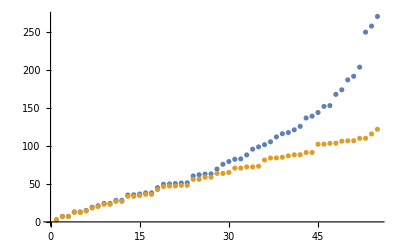

```mathematica
Sort[Abs[eval]/(π^2/4)]
ListPlot[{Sort[Abs[eval]/(π^2/4)],exact}]
```

Defining the eigenbasis

```mathematica
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

{0.270823,Null}

Comparing eigenvalues

```mathematica
AAAA=Sort[Table[(Conjugate[evec].Hfull.Transpose[evec])[[i,i]],{i,1,size}]];
```

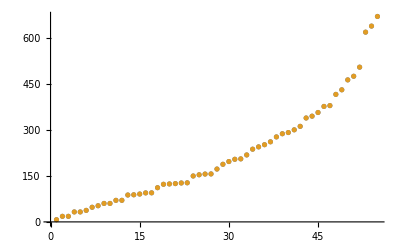

```mathematica
ListPlot[{AAAA,Sort[Re[Abs[eval]]]}]
```

Exporting the data

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[Abs[eval]]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",Table[mode[aa,x,y],{aa,1,size}]]
```

~/agr_tese/data/symbolic_new/schrodinger/hexagon_55/eigenvalues.dat

~/agr_tese/data/symbolic_new/schrodinger/hexagon_55/basis.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_55/eigenvectors.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_55/full_hamiltonian.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_55/eigenfunctions.m

Plotting the eigenfunctions

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```